```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.1,Jtwo,0.1,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.8850612031567836}]
```

{z→0.885061}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.1,l->0.1}
```

0.885061+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.8850612031567836]]
```

{{0.005,0.889544},{0.01,0.89375},{0.015,0.897612},{0.02,0.901046},{0.025,0.903955},{0.03,0.906238},{0.035,0.907803},{0.04,0.908589},{0.045,0.908581},{0.05,0.907813},{0.055,0.906353},{0.06,0.904289},{0.065,0.901709},{0.07,0.898695},{0.075,0.895317},{0.08,0.891634},{0.085,0.887691},{0.09,0.883526},{0.095,0.879171},{0.1,0.874648}}

```mathematica
moduler[Lister[-1,-0.005,0.8850612031567836]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.294377 and 3.20015 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {0.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

{{-0.005,0.880353},{-0.01,0.87546},{-0.015,0.870413},{-0.02,0.865234},{-0.025,0.859941},{-0.03,0.854548},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{-0.065,0},{-0.07,0},{-0.075,0},{-0.08,0},{-0.085,0},{-0.09,0},{-0.095,0},{-0.1,0}}

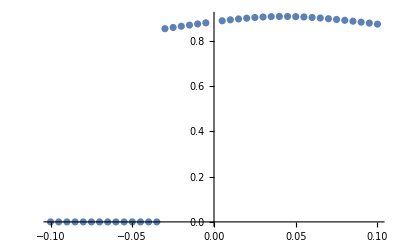

```mathematica
G =ListPlot[{{0.005,0.8895443042880239},{0.01,0.8937501862371299},{0.015,0.8976117128589126},{0.02,0.9010457144558033},{0.025,0.903955250381945},{0.03,0.9062380977141129},{0.035,0.907802760125975},{0.04,0.9085885425445578},{0.045,0.9085807669011964},{0.05,0.9078125774167529},{0.055,0.9063529689145311},{0.06,0.9042887771715518},{0.065,0.901709009606694},{0.07,0.8986952190561132},{0.075,0.895317422521333},{0.08,0.8916335381054745},{0.085,0.8876905267173224},{0.09,0.8835261100279289},{0.095,0.8791705011213276},{0.1,0.874647922175772},{-0.005,0.8803532018936951},{-0.01,0.8754603288389791},{-0.015,0.8704129712336262},{-0.02,0.8652341653660836},{-0.025,0.8599414128474069},{-0.03,0.8545480611725725},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{-0.065,0},{-0.07,0},{-0.075,0},{-0.08,0},{-0.085,0},{-0.09,0},{-0.095,0},{-0.1,0}}]
```

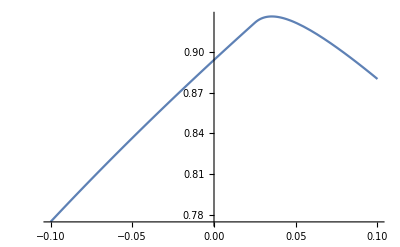

```mathematica
P =Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1}]
```

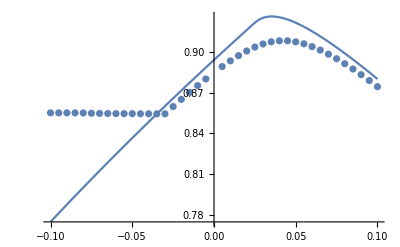

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.1,moduler[Lister[-1,-0.005,0.8850612031567836]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.294377 and 3.20015 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {0.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

{{-0.005,0.00846624},{-0.01,0.00771576},{-0.015,0.00708347},{-0.02,0.00654562},{-0.025,0.00608399},{-0.03,0.00568447},{-0.035,0.8544},{-0.04,0.848528},{-0.045,0.842615},{-0.05,0.83666},{-0.055,0.830662},{-0.06,0.824621},{-0.065,0.818535},{-0.07,0.812404},{-0.075,0.806226},{-0.08,0.8},{-0.085,0.793725},{-0.09,0.787401},{-0.095,0.781025},{-0.1,0.774597}}

```mathematica
differ[1,0.1,moduler[Lister[1,0.005,0.8850612031567836]]]
```

{{0.005,0.0104557},{0.01,0.0117883},{0.015,0.0134316},{0.02,0.0154694},{0.025,0.214079},{0.03,0.0193248},{0.035,0.0187885},{0.04,0.0174244},{0.045,0.0157809},{0.05,0.0141419},{0.055,0.0126386},{0.06,0.0113167},{0.065,0.0101783},{0.07,0.0092066},{0.075,0.00837869},{0.08,0.00767175},{0.085,0.00706544},{0.09,0.00654255},{0.095,0.0060889},{0.1,0.00569292}}

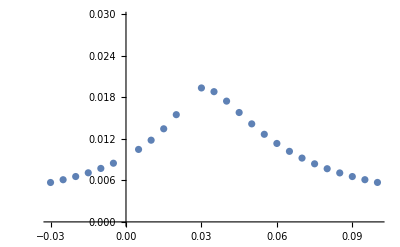

```mathematica
ListPlot[{{-0.005,0.008466239837863765},{-0.01,0.007715757793805622},{-0.015,0.007083467505586083},{-0.02,0.00654562334205111},{-0.025,0.0060839909370317136},{-0.03,0.005684465531690108},{0.005,0.010455695711976132},{0.01,0.011788327576611746},{0.015,0.013431645055517305},{0.02,0.015469424535364706},{0.025,0.21407873836794988},{0.03,0.019324794080208485},{0.035,0.01878853519868351},{0.04,0.01742441632804892},{0.045,0.01578087468960676},{0.05,0.014141868312535832},{0.055,0.012638573236676387},{0.06,0.011316669149806335},{0.065,0.01017829787074953},{0.07,0.009206600683066779},{0.075,0.008378691593730947},{0.08,0.007671749324772881},{0.085,0.007065437383570128},{0.09,0.00654255149331695},{0.095,0.006088901837102312},{0.1,0.005692920907178434}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.87141}. NIntegrate obtained -0.179235 and 0.277837 for the integral and error estimates.

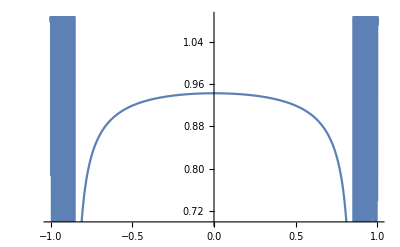

```mathematica
Plot[NullsHolm[-0.035,z],{z,-1,1}]
```